### Setting the Directory

```mathematica
SetDirectory[NotebookDirectory[]];
(*Some unimportant error messages are sw
itched off for future convenience*)
Off[NIntegrate::inumr,FindRoot::lstol,NIntegrate::ncvb];
```

### Various Constants

```mathematica
(* The Subscript[Ω, b] h^2 value from Planck paper - See Table 2, page 16, 4th column of https://arxiv.org/pdf/1807.06209.pdf *)
obh2pl=0.02236;
(* The Subscript[Ω, m] value from Planck paper - See Table 2, page 16, 4th column of https://arxiv.org/pdf/1807.06209.pdf *)
ompl=0.3166;
(* The Subscript[H, 0] value from Planck paper - See Table 2, page 16, 4th column of https://arxiv.org/pdf/1807.06209.pdf *)
H0pl=67.27;
(* The dimensionless parameter for the Hubble constant, defined as Subscript[H, 0]/100 *)
h0pl=H0pl/100;
(* The h value from Type Ia Supernovae - See abstract of https://arxiv.org/pdf/1903.07603.pdf *)
h0riess=0.7403;
(* CMB temperature *)
Tcmb=2.7255;
(* Various constants useful for the following likelihoods *)
c=299792.458;
cH0=2997.92458;
```

### nCPL Model

#### χ^2 Analysis

```mathematica
(* w(a)=Subscript[w, 0]-(Subscript[w, a](1-a))^n, i.e. nCPL model - For n=1 we get the usual CPL model *)
w[a_,w0_,wa_,n_]:=w0+wa (1-a)^n
(* Subscript[f, DE](α) for the nCPL model - See Eq. (4.2) on page 12 from https://arxiv.org/pdf/1603.02164.pdf *)
f[a_,w0_,wa_,n_]:=a^(-3 (1+w0+wa)) ⅇ^(-3 wa HarmonicNumber[n]+3 a n wa HypergeometricPFQ[{1,1,1-n},{2,2},a])
(* Define Subscript[z, equality] and Subscript[a, equality] in order to avoid some problems *)
zeq[om_?NumberQ,h_?NumberQ]:=2.5*10^4 om h^2 (Tcmb/2.7)^-4;
aeq[om_?NumberQ,h_?NumberQ]:=1/(1+zeq[om,h]);
(* E=H/H0 for the nCPL model - See Eq. (4.3) on page 12 from https://arxiv.org/pdf/1603.02164.pdf*) 
H[a_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=100h Sqrt[a^-3 om(1+aeq[om,h]/a)+(1-om(1+aeq[om,h]))f[a,w0,wa,n]]
(* Sound speed - Easily proved from Eq. (3.2) of https://arxiv.org/pdf/1812.05356.pdf *) 
cs[a_?NumberQ,obh2_?NumberQ]:=c/(√(3(1+(31500 obh2(Tcmb/2.7)^-4)a)));
(* Redshift at decoupling - See Eqs. (E-1) on page 33 or see Eqs. (66)-(68) of https://arxiv.org/pdf/0803.0547.pdf on page 30 *)
zcmb[om_?NumberQ,obh2_?NumberQ,h_?NumberQ]:=1048(1+0.00124(obh2)^-0.738)(1+((0.0783(obh2)^-0.238)/(1+39.5(obh2)^0.763))(om h^2)^(0.560/(1+21.1(obh2)^1.81)))
(* Drag redshift - See Eqs. (4) of https://arxiv.org/pdf/astro-ph/9709112.pdf on page 5 *)
zdrag[om_?NumberQ,obh2_?NumberQ,h_?NumberQ]:=1291 ((om h^2)^0.251)/(1+0.659 (om h^2)^0.828)(1+(0.313(om h^2)^-0.419(1+0.607(om h^2)^0.674))(obh2)^(0.238(om h^2)^0.223))
(* Comoving sound horizon at drag redshift - Easily proved from Eq. (3.1) of https://arxiv.org/pdf/1812.05356.pdf *)
rs[ze_,om_?NumberQ,obh2_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=NIntegrate[cs[x,obh2]/(x^2H[x,om,w0,wa,n,h]),{x,10^-11,1/(1+ze[om,obh2,h])}]
(* Luminosity distance Subscript[d, L]- See e.g. Eq. (1.2) from https://arxiv.org/pdf/2004.02155.pdf on page 2 - Define it as it is due to some problems! *)
Clear[DLsol,DL,dL]
DLsol[om_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=(DLsol[om,w0,wa,n,h]=NDSolve[{D[dL[zz]/(1+zz),zz]==1/(H[1/(1+zz),om,w0,wa,n,h]/(100h)),dL[0]==0},dL,{zz,0,1300},MaxSteps->Infinity])
DL[z_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=(c/(100h)dL[z]/.DLsol[om,w0,wa,n,h])[[1]]//Chop
(* Angular diameter distance Subscript[d, A] *)
DA[z_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=DL[z,om,w0,wa,n,h]/(1+z)^2
(* Easily proven from Eq. (3.4) of https://arxiv.org/pdf/1812.05356.pdf *)
Dv[zbao_,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=((DL[zbao,om,w0,wa,n,h]/(1+zbao))^2  (c*zbao)/H[1/(1+zbao),om,w0,wa,n,h])^(1/3)
(* BAO Subscript[d, z] ratio - Subscript[d, z]=Subscript[r, s]/Subscript[D, V] *)
dz[zbao_,om_,obh2_,w0_,wa_,n_,h_]:=rs[zdrag,om,obh2,w0,wa,n,h]/Dv[zbao,om,w0,wa,n,h]
(* Subscript[D, H] "distance" defined as Subscript[D, H](z)=c/(H(z)) - See the end of page 8 from https://arxiv.org/pdf/1812.05356.pdf *)
DH[z_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=c/H[1/(1+z),om,w0,wa,n,h]
hz[z_,om_,w0_,wa_,n_,h_]:=H[1/(1+z),om,w0,wa,n,h]
(* Comoving distance at recombination - Easily proven from Eq. (26) of https://arxiv.org/pdf/1811.07425.pdf on page 7 *)
R[om_,obh2_,w0_,wa_,n_,h_]:=(√(om (100h)^2)DA[zcmb[om,obh2,h],om,w0,wa,n,h](1+zcmb[om,obh2,h]))/c
(* Angular scale of sound horizon at recombination - Easily proven from Eq. (27) of https://arxiv.org/pdf/1811.07425.pdf on page 7  *)
la[om_,obh2_,w0_,wa_,n_,h_]:=(π (DA[zcmb[om,obh2,h],om,w0,wa,n,h](1+zcmb[om,obh2,h])))/rs[zcmb,om,obh2,w0,wa,n,h]
(* H(α) for ΛCDM *)
```

```mathematica
Hlcdm[a_?NumberQ,om_?NumberQ]:=√(om a^-3+(1-om))
Hwcdm[a_?NumberQ,om_?NumberQ,w0_?NumberQ]:=√(om a^-3+(1-om)a^(3*(1+w0)))
(* Luminosity distance Subscript[d, L] *)
(*dLsol[om_?NumberQ]:=(dLsol[om]=NDSolve[{D[dL[zz]/(1+zz),zz]==c/H[1/(1+zz),om],dL[0]==0},dL,{zz,0,1300},AccuracyGoal->5,PrecisionGoal->5,MaxSteps->Infinity])*)
Clear[dL]
DLsolh[om_?NumberQ]:=(DLsolh[om]=NDSolve[{D[dL[zz]/(1+zz),zz]==1/(Hlcdm[1/(1+zz),om]),dL[0]==0},dL,{zz,0,1300},MaxSteps->Infinity])
(* Hubble free luminosity distance Subscript[D, L] *)
DLh[z_?NumberQ,om_?NumberQ]:=(dL[z]/.DLsolh[om])[[1]]//Chop
Clear[dL]
DLsolw[om_?NumberQ,w0_?NumberQ]:=(DLsolw[om,w0]=NDSolve[{D[dL[zz]/(1+zz),zz]==1/(Hwcdm[1/(1+zz),om,w0]),dL[0]==0},dL,{zz,0,1300},MaxSteps->Infinity])
(* Hubble free luminosity distance Subscript[D, L] *)
DLw[z_?NumberQ,om_?NumberQ,w0_?NumberQ]:=(dL[z]/.DLsolw[om,w0])[[1]]//Chop
```

### Data Combination

#### CMB Data

```mathematica
(* Central values for {R, Subscript[l, a], Subscript[Ω, b] h^2} from Planck 2018 for a flat universe - See Eq. (31) of https://arxiv.org/pdf/1811.07425.pdf on page 7 *)
datacmb={1.74963,301.80845,0.02237};
(* Inverse Covariance Matrix using  for {R, Subscript[l, a], Subscript[Ω, b] h^2} *)
covcmb=10^-8({{1598.9554, 17112.007, −36.311179}, {17112.007, 811208.45, −494.79813}, {-36.311179, -494.79813, 2.1242182}});
invcov=Inverse[covcmb];
ndatCMB=Length[datacmb];
(* χ^2 for CMB shift parameters *)
vec[om_,obh2_,w0_,wa_,n_,h_]:={R[om,obh2,w0,wa,n,h]-datacmb[[1]],la[om,obh2,w0,wa,n,h]-datacmb[[2]],obh2-datacmb[[3]]};
chi2R[om_,obh2_,w0_,wa_,n_,h_]:=vec[om,obh2,w0,wa,n,h].invcov.vec[om,obh2,w0,wa,n,h]
```

#### BAO Data

```mathematica
(* 6dFGs and WiggleZ BAO measurements - See page 6 of https://arxiv.org/pdf/1605.02702.pdf *)
databao={{0.106,0.336,0.015},{0.44,0.073,0.031},{0.6,0.0726,0.0164},{0.73,0.0592,0.0185}};
Cijbaoinv=({{1/databao[[1,3]]^2, 0, 0, 0}, {0, 1040.3, -807.5, 336.8}, {0, -807.5, 3720.3, -1551.9}, {0, 336.8, -1551.9, 2914.9}});
(* V^i crucial for the construction of this subset of the BAO χ^2 *)
vecbao[om_,obh2_,w0_,wa_,n_,h_]:=Table[(databao[[i,2]]-dz[databao[[i,1]],om,obh2,w0,wa,n,h]),{i,1,Length[databao]}];
```

```mathematica
(* SDSS BAO measurements from Data Release (DR) 7 and DR11. These measurements correspond to Dv/Subscript[r, d]=Dv/Subscript[r, s] - See abstract of http://arxiv.org/abs/1409.3242 and of https://arxiv.org/abs/1312.4877 respectively *)
dataSDSS={{0.15,4.465666824,0.1681350461},{0.32,8.4673,0.167},{0.57,13.7728,0.134}};
```

```mathematica
(* Ly-α BAO measurements. The first one corresponds to Subscript[D, A]/Subscript[r, d]=Subscript[D, A]/Subscript[r, s] while the second one to Subscript[D, H]/Subscript[r, d]=Subscript[D, H]/Subscript[r, s] - See abstract of https://arxiv.org/abs/1904.03400 *)
dataLya={{2.34,11.2005988024,0.56},{2.34,8.86,0.29}};
CijLyainv=({{1/dataLya[[1,3]]^2, 0}, {0, 1/dataLya[[2,3]]^2}});
(* χ^2 for the Ly-α BAO measurements *)
vecLya[om_,obh2_,w0_,wa_,n_,h_]:={dataLya[[1,2]]-DA[dataLya[[1,1]],om,w0,wa,n,h]/rs[zdrag,om,obh2,w0,wa,n,h],dataLya[[2,2]]-DH[dataLya[[2,1]],om,w0,wa,n,h]/rs[zdrag,om,obh2,w0,wa,n,h]};
(* Length of the BAO data *)
ndatBAO=Length[dataSDSS]+Length[databao]+Length[dataLya];
```

```mathematica
(* Total BAO χ^2 *)
chi2bao[om_,obh2_,w0_,wa_,n_,h_]:=vecbao[om,obh2,w0,wa,n,h].Cijbaoinv.vecbao[om,obh2,w0,wa,n,h]+Sum[(dataSDSS[[i,2]]-1/dz[dataSDSS[[i,1]],om,obh2,w0,wa,n,h])^2/dataSDSS[[i,3]]^2,{i,1,Length[dataSDSS]}]+vecLya[om,obh2,w0,wa,n,h].CijLyainv.vecLya[om,obh2,w0,wa,n,h]
```

#### Full Pantheon Data

```mathematica
(* Import the full Pantheon data. The full (as well as the binned Pantheon) data can be found in https://github.com/dscolnic/Pantheon. Short descriptions in https://archive.stsci.edu/prepds/ps1cosmo/index.html as well as in https://arxiv.org/abs/1710.00845 *)
dataPanth=Import[".\\data\\lcparam_full_long_zhel.txt","Table"];
(* Length of Pantheon data *)
ndatPanth=Length[dataPanth]-1;
(* Import the systematic errors which are in a separate file *)
Dij0=Import[".\\data\\sys_full_long.txt","List"];
Dij=Partition[Dij0[[2;;-1]],{Dij0[[1]]}];
Id=ConstantArray[1,ndatPanth];
(* Construct of the covariance using only the statistical uncertainties *)
Covstat=DiagonalMatrix[dataPanth[[All,6]][[2;;-1]]^2];
(* Construct of the covariance using only the systematic uncertainties *)
Covsys=Dij;
(* Add the two matrices to construct the total one *)
Cijtot=Covsys+Covstat;
InvCovTotal=Inverse[Cijtot];
InvCovstat=Inverse[Covstat];
```

```mathematica
Length[Covstat]
```

1048

```mathematica
(* χ^2 for the Pantheon data. For the theoretical expression of the apparent magnitude m see my Msc diploma thesis as well as Section 2 of https://arxiv.org/pdf/2004.02155.pdf, where we extensively discuss the Pantheon dataset - IMPORTANT: If you want to rewritte the likelihood as a function of ℳ (as discussed in https://arxiv.org/pdf/2004.02155.pdf) you should redefine H function above to avoid some problems (ask me how to do that!) *)
chi2Panth[M_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=
Module[{Δm},
Δm=Table[dataPanth[[1+i,5]]-(M+5 Log10[(1+dataPanth[[1+i,3]])/(1+dataPanth[[1+i,2]])DL[dataPanth[[1+i,2]],om,w0,wa,n,h]]+25),{i,1,ndatPanth}];
Δm.InvCovTotal.Δm]
```

```mathematica
(*wcdm*)
```

```mathematica
chi2Panthstat4[Mcal_?NumberQ,om_?NumberQ,w0_?NumberQ]:= Module[{Δm},
Δm=Table[dataPanth[[1+i,5]]-(5 Log10[(1+dataPanth[[1+i,3]])/(1+dataPanth[[1+i,2]])DLw[dataPanth[[1+i,2]],om,w0]]+Mcal),{i,1,ndatPanth}];
Δm.InvCovTotal.Δm]
```

### Total χ^2

#### χ^2 for ΛCDM, wCDM and CPL models

```mathematica
(* Subscript[χ, tot]^2=Subscript[χ, CMB]^2+Subscript[χ, BAO]^2+Subscript[χ, Panth]^2 - Similarly you can add as many likelihoods as you want! *)
chi2total[M_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,h_?NumberQ]:=chi2R[om,obh2pl,w0,wa,1,h]+chi2bao[om,obh2pl,w0,wa,1,h]+ chi2Panth[M,om,w0,wa,1,h]
(* Total Length of the data *)
ndatot=ndatCMB+ndatBAO+ndatPanth
```

1060

```mathematica
chi2total3[Mcal_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,h_?NumberQ]:=chi2R[om,obh2pl,w0,wa,1,h]+chi2bao[om,obh2pl,w0,wa,1,h]+ chi2Panthstat4[Mcal,om,w0]
```

```mathematica
(*minlcdm2 = FindMinimum[chi2total2[Mcal,om,-1,0,h],{Mcal,23,23.1},{om,0.28,0.29},{h,0.67,0.671}]
```

```mathematica
minlcdm3 = FindMinimum[chi2total3[Mcal,om,w0,0,h],{Mcal,23,23.1},{om,0.28,0.29},{h,0.67,0.671},{w0,-1.2,-1}]
```

{1031.85,{Mcal→23.8121,om→0.328749,h→0.65935,w0→-0.951153}}

```mathematica
Mwcdm = minlcdm3[[2,1,2]];
omwcdm = minlcdm3[[2,2,2]];
wowcdm = minlcdm3[[2,4,2]];
wawcdm  = 0;
hwcdm = minlcdm3[[2,3,2]];
```

```mathematica
dchi[nsig_,M_]:=2 InverseGammaRegularized[M/2,1-Erf[nsig/(√2)]]//N
```

### Errors

```mathematica
chifun2=ListInterpolation[ParallelTable[chi2total3[Mcal,om,w0,0,h],{Mcal,Mwcdm-0.02,Mwcdm+0.02,0.02},{om,omwcdm-0.02,omwcdm+0.02,0.02},{h,hwcdm-0.002,hwcdm+0.002,0.002},{w0,wowcdm-0.002,wowcdm+0.002,0.002},DistributedContexts->Automatic],{{Mwcdm-0.02,Mwcdm+0.02},{omwcdm-0.02,omwcdm+0.02},{hwcdm-0.002,hwcdm+0.002},{wowcdm-0.002,wowcdm+0.002}}];
(* Params that we want to calculate the errors *)
params2={Mcal,om,w0,h};
(* Calculation of the 1σ error according to Eq.(15.3.5) from Numerical Recipes *)
Fij2=1/2 Table[D[chifun2[Mcal,om,h,w0],params2[[p]],params2[[d]]]/.minlcdm3[[2]],{p,1,Length[params2]},{d,1,Length[params2]}];
cij2=Inverse[Fij2];
errors2=Sqrt[Diagonal[cij2]];

Print["The best fit parameters for M , Ω_(0  m), w_0 and h are: M= ",NumberForm[Mwcdm,5]," ± ",NumberForm[errors2[[1]],1]," , Ω_(0  m)= ",NumberForm[omwcdm,3]," ± ",NumberForm[errors2[[2]],2],", w_0= ",NumberForm[wowcdm,3]," ± ",NumberForm[errors2[[3]],2]," and h= ",NumberForm[hwcdm,3]," ± ",NumberForm[errors2[[4]],2]," respectively."]

errors2//MatrixForm
```

ListInterpolation::inhr: Requested order is too high; order has been reduced to {2,2,2,2}.

The best fit parameters for M , Ω_(0  m), w_0 and h are: M= 23.812 ± 0.006 , Ω_(0  m)= 0.329 ± 0.01, w_0= -0.951 ± 0.035 and h= 0.659 ± 0.01 respectively.

(0.00560843
0.0104512
0.034546
0.00998381)

### Contours

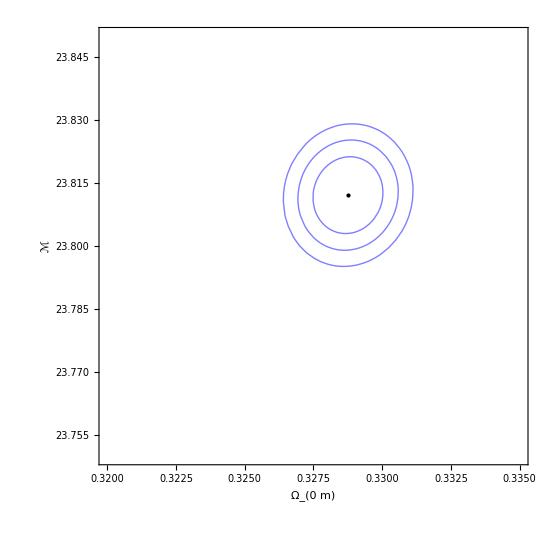

```mathematica
contour15=ContourPlot[chi2total3[Mcal,om,-0.951153342,0,0.659349861],{om,0.320,0.335},{Mcal,23.75,23.85},Contours->{minlcdm3[[1]]+dchi[1,4],minlcdm3[[1]]+dchi[2,4],minlcdm3[[1]]+dchi[3,4]},FrameLabel->{"Ω_(0  m)","ℳ"},BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],Epilog->{{PointSize[Large],Black,Point[{0.3287493611,23.8121285271}]}},ContourShading->False,ContourStyle->Blue,ImageSize->550]
```

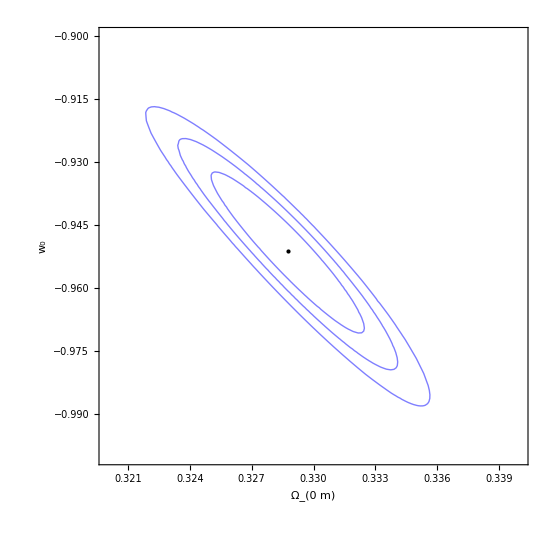

```mathematica
contour16=ContourPlot[chi2total3[23.8121285271,om,w0,0,0.659349861],{om,0.32,0.34},{w0,-1.0,-0.9},Contours->{minlcdm3[[1]]+dchi[1,4],minlcdm3[[1]]+dchi[2,4],minlcdm3[[1]]+dchi[3,4]},FrameLabel->{"Ω_(0  m)","w_0"},BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],Epilog->{{PointSize[Large],Black,Point[{0.3287493611,-0.951153342}]}},ContourShading->False,ContourStyle->Blue,ImageSize->550]
```

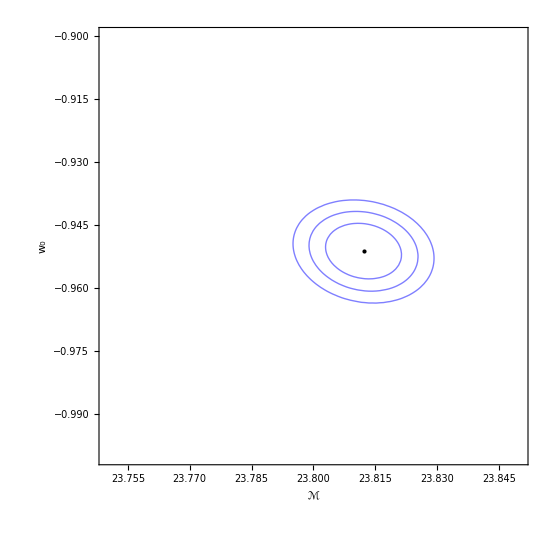

```mathematica
contour17=ContourPlot[chi2total3[Mcal,0.3287493611,w0,0,0.659349861],{Mcal,23.75,23.85},{w0,-1.0,-0.9},Contours->{minlcdm3[[1]]+dchi[1,4],minlcdm3[[1]]+dchi[2,4],minlcdm3[[1]]+dchi[3,4]},FrameLabel->{"ℳ","w_0"},BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],Epilog->{{PointSize[Large],Black,Point[{23.8121285271,-0.951153342}]}},ContourShading->False,ContourStyle->Blue,ImageSize->550]
```

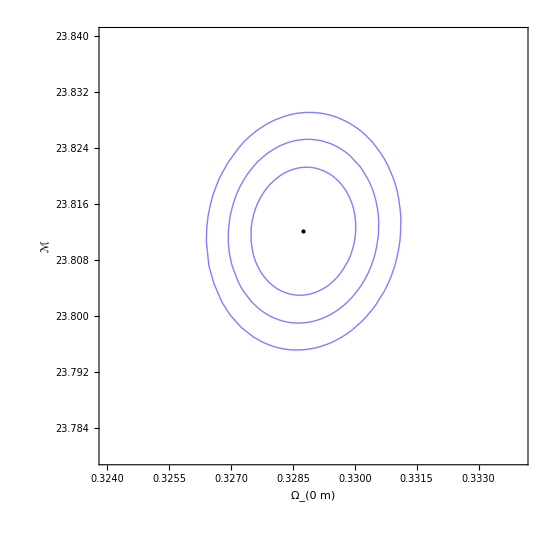

```mathematica
plt1233 = Show[contour15,PlotRange->{{0.324,0.334},{23.78,23.84}} ]
```

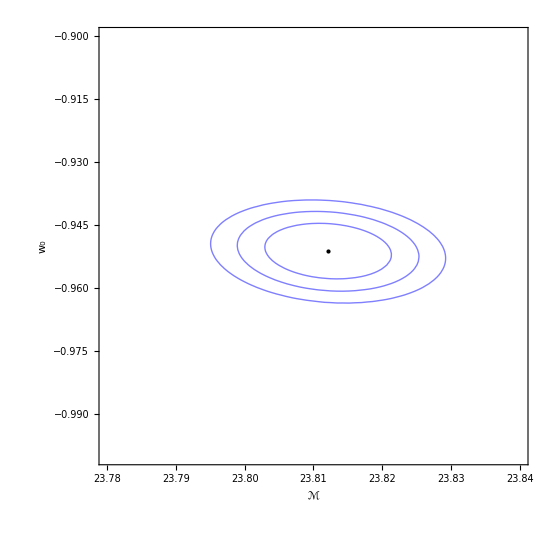

```mathematica
plt1234 = Show[contour17,PlotRange->{{23.78,23.84},{-1,-0.90}} ]
```

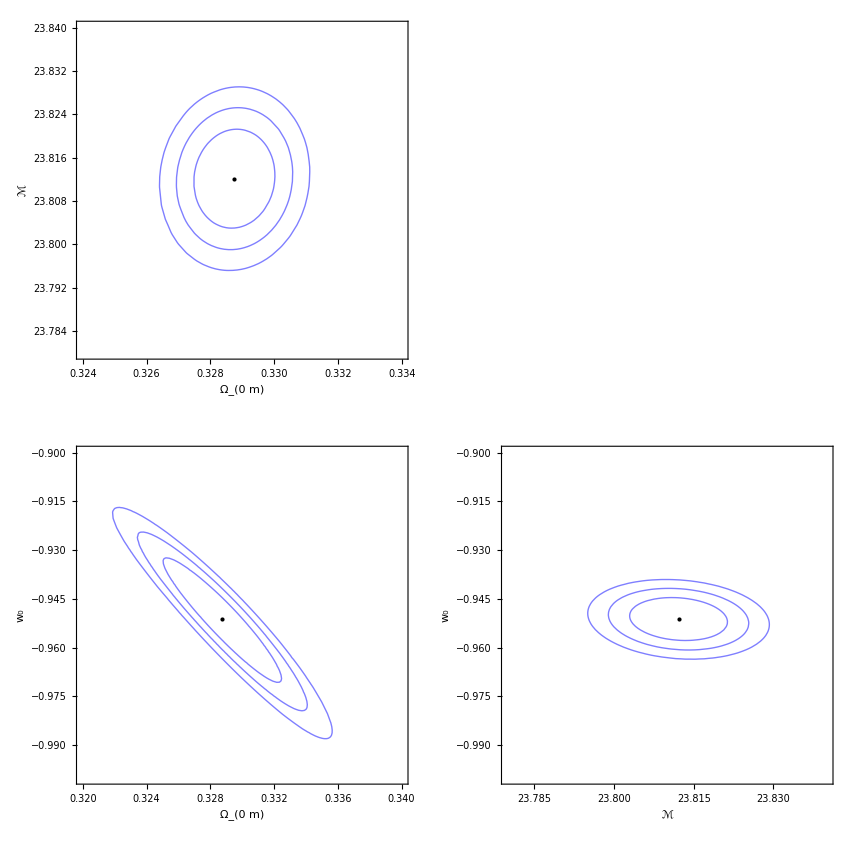

```mathematica
fig4=GraphicsGrid[{{plt1233},{contour16,plt1234}},Spacings->0,ImageSize->850]
```